## Section | Anharmonic Oscillator

A general method for finding approximate solutions to self-adjoint second-order eigenvalue problems of the form

L[y]=(p y')'-(q y)-λ y,  L[y][x]=0,

satisfying homogenous boundary conditions

y(x_0)=0=y(x_1),

is the Rayleigh-Ritz variational technique which consists of determining the constants c_i, i=0,1,…,n-1, in the approximate solution

y≈y_n(x)=∑_(i=0)^(n-1) c_i v_i(x)≡c.v(x),

by solving the Ritz (matrix) equation

𝒜.c=λ ℬ.c,

where {c}_i=c_i with 𝒜 defined by

{𝒜}_(i,j)=α_(i,j)=α_(j,i)=∫_x_0^x_1 (p(x) v'_i(x) v'_j(x)+q(x) v_i(x) v_j(x))ⅆx,

and the overlap matrix

{ℬ}_(i,j)=β_(i,j)=β_(j,i)=∫_x_0^x_1 v_i(x) v_j(x) ⅆx.

The generalized eigenvalue problem (Section.Equation) can be solved (for non-singular ℬ) using (ℬ^-1.𝒜).c=λ c.

The Schrödinger equation for the harmomic oscillator (HO) with a quartic (anharmonic) perturbation can be written in the form

ψ''(x)+(ϵ-x^2-γ x^4) ψ(x)==0,

with boundary conditions

ψ(-∞)=0=ψ(∞).

Consider finding approximate solutions to (Section.Equation) using the basis functions ψ_i(x), i=0,1,…,n-1,

```mathematica
Subscript[ψ, i_](x_)=x^i ⅇ^(-x^2/2);
```

Section.Exercise. Verify that the first few basis functions, ψ_i(x), satisify the boundary conditions (Section.Equation). [2]

```mathematica
Table(lim_(x->∞) Subscript[ψ, i](x),{i,0,5})
```

{0,0,0,0,0,0}

```mathematica
Table(lim_(x->-∞) Subscript[ψ, i](x),{i,0,5})
```

{0,0,0,0,0,0}

Section.Exercise. Verify that ψ_0(x) satisifies (Section.Equation) for γ=0 and find the corresponding (energy) eigenvalue ϵ_0. [2]

```mathematica
Subscript[ψ, 0]''(x)+(Subscript[ϵ, 0]-x^2)Subscript[ψ, 0](x)//Factor
```

ⅇ^(-x^2/2) (-1+ϵ_0)

From this ϵ_0=1.

Section.Exercise. By comparing (Section.Equation) with (Section.Equation) define code for computing the functions p(x) and q_γ(x). [2]

By identification

```mathematica
p(x_)=1;Subscript[q, γ_](x_)=x^2+γ x^4;
```

Section.Exercise. Define code for computing the (n×n) matrices 𝒜_n(γ) defined by (Section.Equation) and the overlap matrix ℬ_n defined by (Section.Equation).  [5]

The Ritz matrix 𝒜_n(γ), computable in closed form, reads

```mathematica
Subscript[𝒜, n_](γ_):=Table(Subscript[α, i,j][γ],{i,0,n-1},{j,0,n-1})
```

The problem is that this expression is that, taking appropriate limits is required. But here is a way around this:

```mathematica
∫_(-∞)^∞ (p(x) Subscript[ψ, i]'(x) Subscript[ψ, j]'(x)+Subscript[q, γ](x) Subscript[ψ, i](x) Subscript[ψ, j](x))ⅆx
```

ConditionalExpression[1/16 (1+(-1)^(i+j)) (4 (-1+i+j+2 i j)+(-1+i+j) (1+i+j) (3+i+j) γ) Gamma[1/2 (-1+i+j)], Re[i+j]>1]

```mathematica
1/2 (1+(-1)^(i+j)) (i j Γ(1/2 (i+j-1))-(i+j) Γ(1/2 (i+j+1))+Γ(1/2 (i+j+3))+γ Γ(1/2 (i+j+5)))
```

1/2 ((-1)^(i+j)+1) (γ 1/2 (i+j+5)+i j 1/2 (i+j-1)-(i+j) 1/2 (i+j+1)+1/2 (i+j+3))

```mathematica
i j 1/2 (i+j-1)/.{i->0,j->1}
```

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
i j 1/2 (i+j-1)j1i0
```

2

```mathematica
i j 1/2 (i+j-1)j0i1
```

0

#### Steps

```mathematica
Clear@α
```

```mathematica
α/:Subscript[α, i_,j_]:=α/:Subscript[α, i,j]=γ↦Evaluate[∫_(-∞)^∞ (p(x) Subscript[ψ, i]'(x) Subscript[ψ, j]'(x)+Subscript[q, γ](x) Subscript[ψ, i](x) Subscript[ψ, j](x))ⅆx]
```

```mathematica
Subscript[α, 0,0](γ)
```

1/4 √π (4+3 γ)

```mathematica
Subscript[α, 1,0](γ)
```

0

```mathematica
Subscript[α, 0,1](γ)
```

0

```mathematica
Subscript[α, 1,1](γ)
```

3/8 √π (4+5 γ)

```mathematica
?α
```

#### General

```mathematica
α/:Subscript[α, i_,j_]=γ↦Evaluate[∫_(-∞)^∞ (p(x) Subscript[ψ, i]'(x) Subscript[ψ, j]'(x)+Subscript[q, γ](x) Subscript[ψ, i](x) Subscript[ψ, j](x))ⅆx];
```

```mathematica
?α
```

#### Overlap matrix

The overlap matrix ℬ_n is

```mathematica
Clear@ℬ
```

```mathematica
ℬ/:Subscript[ℬ, n_]:=Table(Subscript[β, i,j],{i,0,n-1},{j,0,n-1})
```

```mathematica
β/:Subscript[β, i_,j_]=∫_(-∞)^∞ Subscript[ψ, i](x) Subscript[ψ, j](x)ⅆx
```

ConditionalExpression[1/2 (1+(-1)^(i+j)) Gamma[1/2 (1+i+j)], Re[i+j]>-1]

Section.Exercise. When there is no anharmonic term (i.e., γ=0) the exact eigenvalues are ϵ_i=2i+1. Compute the set of (numerical) eigenvalues, {λ_i}, and corresponding eigenvectors, {c_i}, of ℬ_n^-1.𝒜_n(0) for n=10.  Compare each ϵ_i with the corresponding (ordered) λ_i. [4]

Using Eigensystem we get the set of eigenvalues Λ={λ_i}_(i=0,1,…,n-1) and corresponding eigenvectors P={c_i}_(i=0,1,…,n-1):

```mathematica
({Λ,P}=Reverse/@Chop[Eigensystem[(N[Subscript[ℬ, 20],50]^-1).Subscript[𝒜, 20](1`50)]])^T;
```

```mathematica
Λ⟦Range[5]⟧
```

{1.39235391952080653059786655606277646,4.64881874667480106980929549003250538,8.65535014698976221023850896184881766,13.1589571287068437957121274069869783,18.0641957192354642514325793324987431}

Section.Exercise. Using the eigenvectors, {c}, obtained in Section.Exercise compute the approximate eigenfunctions, ψ(x), via (Section.Equation) and normalise each according to 1=∫_(-∞)^∞ (ψ(x))^*ψ(x)ⅆx=∑_(i,j) c_i β_(i,j)c_j≡c.ℬ.c. Plot the 5 lowest energy (normalised) eigenfunctions, each shifted upwards by their energy, superimposed onto a plot of the potential q_0(x). [6]

We normalise the each eigenvector c by dividing by √(c.ℬ_n.c) and compute the approximate eigenfunctions using (Section.Equation):

```mathematica
efns[P_]:=With[{n=Length[P]},(P.Table(Subscript[ψ, i](x),{i,0,n-1}))/(√Transpose[P.Subscript[ℬ, n].P^T,{1,1}])//Simplify]
```

Here is a plot of the 5 lowest energy eigenfunctions, each shifted upwards by (twice) their energy, Λ, superimposed onto a plot of the potential q_0(x):

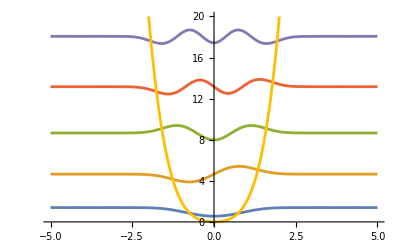

```mathematica
Plot[Evaluate[Join[(Λ+efns[P])[[;;7]],{Subscript[q, 1][x]}]],{x,-5,5},PlotRange->{0,20}]
```

Note that the eigenfunctions have an inflection point (near?) where they intersect the potential curve.

Section.Exercise. Compute the anharmonic eigenfunctions for n=10 with γ=0.1.  Plot the 5 lowest energy normalised eigenfunctions, compare with the result of Section.Exercise, and comment. Show graphically how well the anharmonic eigenfunctions satisfy the Schrödinger equation (Section.Equation).  [9]

```mathematica
({Λ,P}=Reverse/@Chop[Eigensystem[(Subscript[ℬ, 10]^-1).Subscript[𝒜, 10](0.1)]])^T;
```

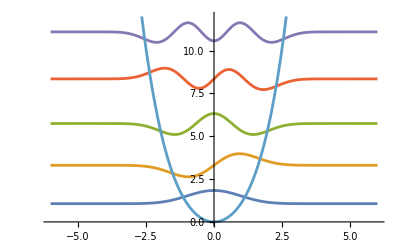

```mathematica
Plot[Evaluate[Join[(Λ+efns[P])[[;;6]],{Subscript[q, 0.1][x]}]],{x,-6,6},PlotRange->{0,12}]
```

```mathematica
({Λ,P}=Reverse/@Chop[Eigensystem[(Subscript[ℬ, 10]^-1).Subscript[𝒜, 10](0)]])^T;
```

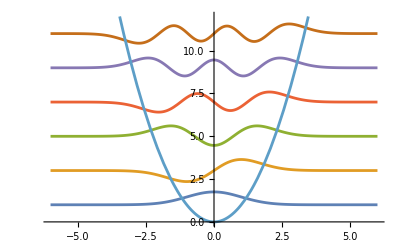

```mathematica
harmonic=Plot[Evaluate[Join[(Λ+efns[P])[[;;6]],{Subscript[q, 0][x]}]],{x,-6,6},PlotRange->{0,12}]
```

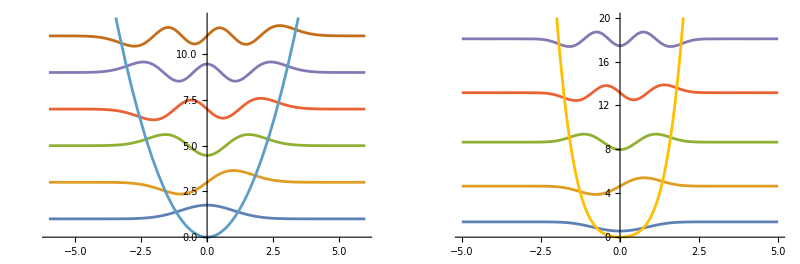

```mathematica
GraphicsRow[{harmonic,anharmonic}]
```

The potential is symmetric about x=0 in both cases and this is reflected in the eigenfunctions which are alternately even and odd functions.  It is clear that the energy of each anharmonic function is greater than the corresponding harmonic function.

Substituting the (set of) normalised eigenfunctions back into the Schrödinger equation (Section.Equation):

```mathematica
({Λ,P}=Reverse/@Chop[Eigensystem[(Subscript[ℬ, 10]^-1).Subscript[𝒜, 10](0.1)]])^T;
```

here is a plot of how well the first eigenfunction satisifies the differential equation:

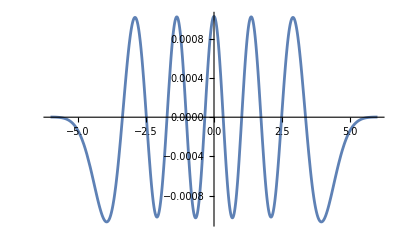

```mathematica
Plot[Evaluate[((∂^2 efns(P))/(∂x^2)+ (Λ-Subscript[q, 0.1](x))efns(P))⟦1⟧],{x,-6,6}]
```

Section.Exercise. Consider the quartic oscillator  [9]

```mathematica
n=.
```

```mathematica
Subscript[α, 0,j_](γ_)=.
```

```mathematica
Subscript[α, j_,0](γ_)=.
```

```mathematica
p(x_)=1;Subscript[q, γ_](x_)=γ x^4;
```

```mathematica
Subscript[ψ, n_](x_)=ⅇ^(-x^2/2)Subscript[H, n](x);
```

```mathematica
Subscript[β, i_,j_]=i! 2^i √π Subscript[δ, i,j];
```

```mathematica
p(x) Subscript[ψ, i]'(x) Subscript[ψ, j]'(x)+Subscript[q, γ](x) Subscript[ψ, i](x) Subscript[ψ, j](x)//Factor
```

ⅇ^(-x^2) (γ H_i(x) H_j(x) x^4+H_i(x) H_j(x) x^2-2 j H_i(x) H_(j-1)(x) x-2 i H_(i-1)(x) H_j(x) x+4 i j H_(i-1)(x) H_(j-1)(x))

The two-term recursion relation for the Hermite polynomials reads

H_n(x)=2 x H_(n-1)(x)-2 (n-1) H_(n-2)(x), n≥1

```mathematica
Collect[Expand[%//.Subscript[H, n_](x) x^(i_.):>n Subscript[H, n-1](x) x^(i-1)+1/2 Subscript[H, n+1](x) x^(i-1)],Subscript[H, i_](x)Subscript[H, j_](x),Factor]
```

2 ⅇ^(-x^2) i j H_(i-1)(x) H_(j-1)(x)-ⅇ^(-x^2) j H_(i+1)(x) H_(j-1)(x)+ⅇ^(-x^2) (i-3) (i-2) (i-1) i γ H_(i-4)(x) H_j(x)+ⅇ^(-x^2) (i-1) i (2 i γ-γ-1) H_(i-2)(x) H_j(x)+1/4 ⅇ^(-x^2) (6 γ i^2+6 γ i+3 γ+2) H_i(x) H_j(x)+1/4 ⅇ^(-x^2) (2 i γ+3 γ+1) H_(i+2)(x) H_j(x)+1/16 ⅇ^(-x^2) γ H_(i+4)(x) H_j(x)

```mathematica
Subscript[α, i_,j_](γ_)=i! 2^i √π Collect[%/(i! 2^i √π)/.ⅇ^(-x^2) Subscript[H, i_](x) Subscript[H, j_](x)->i! 2^i √π Subscript[δ, i,j],Subscript[δ, i_,j_],FunctionExpand]
```

2^i √π i! (1/16 γ δ_(i-4,j)+1/4 (2 i γ-γ-1) δ_(i-2,j)+j δ_(i-1,j-1)+1/4 (6 γ i^2+6 γ i+3 γ+2) δ_(i,j)-2 (i+1) j δ_(i+1,j-1)+(i+1) (i+2) (2 i γ+3 γ+1) δ_(i+2,j)+(i+1) (i+2) (i+3) (i+4) γ δ_(i+4,j))

```mathematica
({Λ,P}=Reverse/@Eigensystem[(Subscript[ℬ, 50]^-1).Subscript[𝒜, 50](1`40)])^T;
```

```mathematica
efns=ψ/@P;
```

```mathematica
Λ⟦1⟧
```

1.06036209048454510534546867909110871035

```mathematica
anharmonic=Plot(Evaluate(Take(efns+Λ,6)),{x,-3,3},PlotStyle->Table(Hue(i/6),{i,6}),PlotRange->{0,22},Epilog->(Plot(Subscript[q, 1](x),{x,-3,3},DisplayFunction->Identity))⟦1⟧);
```

The potential is symmetric about x=0 in both cases and this is reflected in the eigenfunctions which are alternately even and odd functions.

Substituting the (set of) normalised eigenfunctions back into the Schrödinger equation (Section.Equation):

```mathematica
(∂^2 efns[P])/(∂x^2)+ (Λ-Subscript[q, 1](x))efns[P];
```

here is a plot of how well the first eigenfunction satisifies the differential equation:

```mathematica
Plot(Evaluate[%⟦1⟧],{x,-6,6});
```

### Section. The New Algorithm

To get a very high–precision approximation of

-ψ''(x)+x^4 ψ(x)=λ ψ(x)

we start with the series expansion

ψ(x)=y_n(x)=∑_(k=0)^n a_k(λ)x^k

For the ground state we choose (ignoring normalization) ψ(0)=1, ψ'(0)=0. For “suitable chosen” x^* we then find high–precision approximations for the zeros of y_n(x^*) and y'_n(x^*). These zeros then bound λ_0 from below and above.

Using the differential equation one obtains the following recursion relation for the a_k(λ):

```mathematica
-ψ''(x)+x^4 ψ(x)-λ ψ(x)/.ψ->Function[x,Subscript[a, k](λ)x^k]
```

-(k-1) k a_k(λ) x^(k-2)-λ a_k(λ) x^k+a_k(λ) x^(k+4)

```mathematica
%/.c_ x^(k+a_):>(c/.k->k-a)x^k//Factor//FullSimplify
```

x^k (a_(k-4)(λ)-λ a_k(λ)-(k+1) (k+2) a_(k+2)(λ))

```mathematica
Last[%]/.k->k-2
```

a_(k-6)(λ)-λ a_(k-2)(λ)-(k-1) k a_k(λ)

```mathematica
Solve[%==0,Subscript[a, k](λ)]//First//First//Simplify
```

a_k(λ)→(a_(k-6)(λ)-λ a_(k-2)(λ))/(k^2-k)

The calculation of y_n(x) and y'_n(x) is also straightforward based on a recursive calculations of the a_k(λ).

```mathematica
Clear[a]
```

```mathematica
a/:Subscript[a, k_/;k<0]=Function[λ,0];
```

```mathematica
a/:Subscript[a, 0]=Function[λ,1];
```

```mathematica
a/:Subscript[a, 1]=Function[λ,0];
```

```mathematica
a/:Subscript[a, k_]:=(a/:Subscript[a, k]=Function[λ,Evaluate[Simplify[(Subscript[a, k-6](λ)-λ Subscript[a, k-2](λ))/(k^2-k)]]])
```

```mathematica
Table[{k,Subscript[a, k](λ)},{k,0,20}]
```

(0 | 1
1 | 0
2 | -λ/2
3 | 0
4 | λ^2/24
5 | 0
6 | 1/720 (24-λ^3)
7 | 0
8 | (λ (λ^3-384))/40320
9 | 0
10 | -(λ^2 (λ^3-2064))/3628800
11 | 0
12 | (λ^6-7104 λ^3+120960)/479001600
13 | 0
14 | -(λ (λ^6-18984 λ^3+4682880))/87178291200
15 | 0
16 | (λ^2 (λ^6-43008 λ^3+54268416))/20922789888000
17 | 0
18 | (-λ^9+86688 λ^6-364571136 λ^3+5283532800)/6402373705728000
19 | 0
20 | (λ (λ^9-160128 λ^6+1758756096 λ^3-349194240000))/2432902008176640000)

a_k(λ)  =(a_(k-6)(λ)-λ a_(k-2)(λ))/(k^2-k)

For large n (n→∞) we want the function y_n(x) to vanish as x→∞. For a λ smaller than the smallest possible λ, the function y_n(x^*) will not have a zero, but the function y'_n(x^*) will have a zero for  a certain x^*. For a λ larger then the smallest possible λ, the function y_n(x^*) will have a zero, but the function y'_n(x^*) will not have a zero for a certain x^*. This allows to find a bounding interval for λ_0. The next two graphics show y_80(x) and y'_80(x) for 10 equidistant values for λ from the interval [1.05,1.08] to visualize this bounding process.

```mathematica
Subscript[y, n_][λ_][x_]:=∑_(k=0)^n Subscript[a, k](λ)x^k
```

```mathematica
Plot[Evaluate[Table[Subscript[y, 80][λ][x],{λ,1.05,1.08,(1.08-1.05)/9}]],{x,0,3},PlotStyle->Table[Hue[i/10],{i,10}]];
```

```mathematica
Plot[Evaluate[Table[Subscript[y, 80][λ]'[x],{λ,1.05,1.08,(1.08-1.05)/9}]],{x,0,3},PlotStyle->Table[Hue[i/10],{i,10}]];
```

```mathematica
Table[{λ,x/.Flatten[RootsInRange[Subscript[y, 80][λ][x],{x,0,3},DisplayFunction->Identity]],x/.Flatten[RootsInRange[Subscript[y, 80][λ]'[x],{x,0,3},DisplayFunction->Identity]]},{λ,1.05,1.08,(1.08-1.05)/9}]
```

(1.05 | x | 2.05475
1.05333 | x | 2.09969
1.05667 | x | 2.17021
1.06 | x | 2.39358
1.06333 | 2.17005 | x
1.06667 | 2.08353 | x
1.07 | 2.03107 | x
1.07333 | 1.99254 | x
1.07667 | 1.96173 | x
1.08 | 1.93589 | x)

It is straightforward to implement the calculation of the bounding interval for λ_0 in Mathematica in a three–line program. Using FindRoot we calculate high–precision values for the zeros of y_n(ξ) and y'_n(ξ).

```mathematica
λBounds(n_,x_,opts___):=λ/.{FindRoot[Evaluate[Subscript[y, n][λ][x]]==0,{λ,106/100,107/100},opts],FindRoot[Evaluate[Subscript[y, n][λ]'[x]]==0,{λ,106/100,107/100},opts]}//Sort
```

```mathematica
λBounds[40,2]
```

{1.0441,1.07262}

```mathematica
λBounds(100,3,WorkingPrecision->600,AccuracyGoal->60,MaxIterations->100)
```

{1.060362036707059672699809724016451395531677565394701979460378375964200682567443663892570301174415337345733168248868952367528245066085784752081795721059839211814751036872202217208722876726761683384,1.060362139875953880079207847055462156054979661773975275254384014290576278511289492985350938068549974384614741842394713194562930680093824024930375008249965119137180970968517962685252048063263746698}

```mathematica
λBounds(200,3,WorkingPrecision->600,AccuracyGoal->60,MaxIterations->100)
```

{1.060362037084543847537461886445232849358477742012956383280994858440134568940041900358513266945990347366886418215662469196086890493077697551140677085973057072685911760175270990495946039617041682406,1.060362139972967736810136864277602601419096886186301033155110208717580762275242162094777846423638672076520379963741847281704839141746907149266334705873357363364751028600637957602117496799520679289}

Calculating now λBounds[16000, 16, startingValues, WorkingPrecision→6000, AccuracyGoal→600, MaxIterations→100] (where startingValues has been obtained from a call to λBounds recursively, one gets in a few minutes a 1184 digit approximation to the ground state energy of the quartic anharmonic oscillator.

ε_0=1.060362090484182899647046016692663545515208728528977933216245241695943563044344421126896299134671703510546244358582525580879808210293147013176836373824935789226246004708175446960141637488417282256905935757790888061788790263601549395690275196148900942934873584409442694897901213971464290951923354533828347033505757615112025703988852372024022184110308657373109139891545365841031116794058335486000922744006963112670238862297142969961059215583226671376935508673610000831830027517926233573913906136180776498596961814994127928092728407079561060440722946809949136275729273872791368902798424722261716944488954751370438068405439187787729532342458743725431783231906038106874160440343745301468472781391861294047043103401351071607110353008929823275427661518986950565047160252756089526262191025688200964410287815640052705292932405076382650282591124773625384718547144025722854384852974504585709788402490669995704768445877091762029124375273254907116433440230294730692398190895685374535988446016002313291933059395869304916644281633946163324287004261461237743009952234204208597735690153565416850308941851348795734106585479719467596466796613467688586437952654519560568286715958338884743467012042420714919290048732…

Statistical analysis of the number does not show any regularity.